```mathematica
SetDirectory["~/SDPBootstrap"];
(* ::Package::*)(*Setup*)prec=200;

(*A matrix with constant anti-diagonals given by the list bs*)
antiBandMatrix[bs_]:=Module[{n=Ceiling[Length[bs]/2]},Reverse[Normal[SparseArray[Join[Table[Band[{i,1}]->bs[[n-i+1]],{i,n}],Table[Band[{1,i}]->bs[[n+i-1]],{i,2,n}]],{n,n}]]]];

(*DampedRational[c,{p1,p2,...},b,x] stands for c b^x/((x-p1)(x-p2)...)*)
(*It satisfies the following identities*)

DampedRational[const_,poles_,base_,x+a_]:=DampedRational[base^a const,#-a&/@poles,base,x];

DampedRational[const_,poles_,base_,a_/;FreeQ[a,x]]:=const base^a/Product[a-p,{p,poles}];

DampedRational/:x DampedRational[const_,poles_/;MemberQ[poles,0],base_,x]:=DampedRational[const,DeleteCases[poles,0],base,x];

DampedRational/:DampedRational[c1_,p1_,b1_,x] DampedRational[c2_,p2_,b2_,x]:=DampedRational[c1 c2,Join[p1,p2],b1 b2,x];

DampedRational/:a_ DampedRational[c_,p_,b_,x]/;FreeQ[a,x]:=DampedRational[a c,p,b,x];

(*bilinearForm[f,m]=Integral[x^m f[x],{x,0,Infinity}]*)
(*The special case when f[x] has no poles*)
bilinearForm[DampedRational[const_,{},base_,x],m_]:=const Gamma[1+m] (-Log[base])^(-1-m);

(*memoizeGamma[a_,b_]:=memoizeGamma[a,b]=Gamma[a,b];*)

(*The case where f[x] has only single poles*)
(*bilinearForm[DampedRational[const_,poles_,base_,x],m_]:=const Sum[((-poles[[i]])^m) (base^poles[[i]]) Gamma[1+m] memoizeGamma[-m,poles[[i]] Log[base]]/Product[poles[[i]]-p,{p,Delete[poles,i]}],{i,Length[poles]}];*)

(*The case where f[x] can have single or double poles*)
(*bilinearForm[DampedRational[c_,poles_,b_,x_],m_]:=Module[{gatheredPoles=Gather[poles],quotientCoeffs=CoefficientList[PolynomialQuotient[x^m,Product[x-p,{p,poles}],x],x],integral,p,rest},integral[a_,1]:=b^a Gamma[0,a Log[b]];
integral[a_,2]:=-1/a+b^a Gamma[0,a Log[b]] Log[b];
c (Sum[p=gatheredPoles[[n,1]];
rest=x^m/Product[x-q,{q,Join@@Delete[gatheredPoles,n]}];
Switch[Length[gatheredPoles[[n]]],1,integral[p,1] rest/. x->p,2,integral[p,2] rest+integral[p,1] D[rest,x]/. x->p],{n,Length[gatheredPoles]}]+Sum[quotientCoeffs[[n+1]] Gamma[1+n] (-Log[b])^(-1-n),{n,0,Length[quotientCoeffs]-1}])];*)

(*A bilinearForm that allows for arbitrary collections of poles*)
bilinearForm[DampedRational[c_,poles_,b_,x_],m_]:=Module[{gatheredPoles=GatherBy[poles,Round[#,10^(-prec/2)]&],quotientCoeffs=CoefficientList[PolynomialQuotient[x^m,Product[x-p,{p,poles}],x],x],integral,rest,logRest,p,otherPoles,l},integral[0]:=b^x Gamma[0,x Log[b]];
integral[k_]:=integral[k]=Simplify[D[integral[k-1],x]/k];
dExp[k_]:=dExp[k]=Expand[E^(-f[x])D[E^(f[x]),{x,k}]];
c (Sum[p=gatheredPoles[[n,1]];
l=Length[gatheredPoles[[n]]];
Clear[otherPoles,logRest,rest];
otherPoles=Join@@Delete[gatheredPoles,n];
logRest[k_]:=logRest[k]=(k-1)! (-1)^(k-1) (m/p^k-Sum[1/(p-q)^k,{q,otherPoles}]);
rest[k_]:=(dExp[k]/. {Derivative[n_][f][x]:>logRest[n]})/k!;
p^m/Product[p-q,{q,otherPoles}]*Sum[(integral[l-k-1]/.x->p)*rest[k],{k,0,l-1}],{n,Length[gatheredPoles]}]+Sum[quotientCoeffs[[n+1]] Gamma[1+n] (-Log[b])^(-1-n),{n,0,Length[quotientCoeffs]-1}])];

(*orthogonalPolynomials[f,n] is a set of polynomials with degree 0 through n which are orthogonal with respect to the measure f[x] dx*)
orthogonalPolynomials[const_/;FreeQ[const,x],0]:={1/Sqrt[const]};

orthogonalPolynomials[const_/;FreeQ[const,x],degree_]:=error["can't get orthogonal polynomials of nonzero degree for constant measure"];

orthogonalPolynomials[DampedRational[const_,poles_,base_,x],degree_]:=Table[x^m,{m,0,degree}].Inverse[CholeskyDecomposition[antiBandMatrix[Table[bilinearForm[DampedRational[const,Select[poles,#<0&],base,x],m],{m,0,2 degree}]]]];

(*Preparing SDP for Export*)
rhoCrossing=SetPrecision[3-2 Sqrt[2],prec];

rescaledLaguerreSamplePoints[n_]:=Table[SetPrecision[π^2 (-1+4k)^2/(-64n Log[rhoCrossing]),prec],{k,0,n-1}];

maxIndexBy[l_,f_]:=SortBy[Transpose[{l,Range[Length[l]]}],-f[First[#]]&][[1,2]];

(*finds v' such that a.v=First[v']+a'.Rest[v'] when normalization.a==1,where a' is a vector of length one less than a*)
reshuffleWithNormalization[normalization_,v_]:=Module[{j=maxIndexBy[normalization,Abs],const},const=v[[j]]/normalization[[j]];
Prepend[Delete[v-normalization*const,j],const]];

(*XML Exporting*)
nf[x_Integer]:=x;
nf[x_]:=NumberForm[SetPrecision[x,prec],prec,ExponentFunction->(Null&)];

safeCoefficientList[p_,x_]:=Module[{coeffs=CoefficientList[p,x]},If[Length[coeffs]>0,coeffs,{0}]];

WriteBootstrapSDP[file_,SDP[objective_,normalization_,positiveMatricesWithPrefactors_],samplePointsFn_:rescaledLaguerreSamplePoints]:=Module[{stream=OpenWrite[file],node,real,int,vector,polynomial,polynomialVector,polynomialVectorMatrix,affineObjective,polynomialVectorMatrices},(*write a single XML node to file.children is a routine that writes child nodes when run.*)node[name_,children_]:=(WriteString[stream,"<",name,">"];
children[];
WriteString[stream,"</",name,">\n"];);
real[r_][]:=WriteString[stream,nf[r]];
int[i_][]:=WriteString[stream,i];
vector[v_][]:=Do[node["elt",real[c]],{c,v}];
polynomial[p_][]:=Do[node["coeff",real[c]],{c,safeCoefficientList[p,x]}];
polynomialVector[v_][]:=Do[node["polynomial",polynomial[p]],{p,v}];
polynomialVectorMatrix[PositiveMatrixWithPrefactor[prefactor_,m_]][]:=Module[{degree=Max[Exponent[m,x]],samplePoints,sampleScalings,bilinearBasis},samplePoints=samplePointsFn[degree+1];
sampleScalings=Table[prefactor/. x->a,{a,samplePoints}];
bilinearBasis=orthogonalPolynomials[prefactor,Floor[degree/2]];
node["rows",int[Length[m]]];
node["cols",int[Length[First[m]]]];
node["elements",Function[{},Do[node["polynomialVector",polynomialVector[reshuffleWithNormalization[normalization,pv]]],{row,m},{pv,row}]]];
node["samplePoints",vector[samplePoints]];
node["sampleScalings",vector[sampleScalings]];
node["bilinearBasis",polynomialVector[bilinearBasis]];];
node["sdp",Function[{},node["objective",vector[reshuffleWithNormalization[normalization,objective]]];
node["polynomialVectorMatrices",Function[{},Do[node["polynomialVectorMatrix",polynomialVectorMatrix[pvm]],{pvm,positiveMatricesWithPrefactors}];]];]];
Close[stream];];
```

## Examples

```mathematica
(*The following is the example in the manual*)
(*Maximize {a,b}.{0,-1}=-b over {a,b} such that {a,b}.{1,0}=a=1 and E^(-x)(a(1+x^4)+b(x^4/12+x^2))>=0 for all x>=0 Equivalently,1+x^4+b(x^4/12+x^2)>=0 for all x>=0 The prefactor DampedRational[1,{},1/E,x] doesn't affect the answer,but does affect the choice of sample scalings and bilinear basis.*)
testSDP[datFile_]:=Module[{pols={PositiveMatrixWithPrefactor[DampedRational[1,{},1/E,x],{{{1+x^4,x^4/12+x^2}}}]},norm={1,0},obj={0,-1}},WriteBootstrapSDP[datFile,SDP[obj,norm,pols]];];
fname = FileNameJoin[{Directory[], "test"}]
testSDP[fname]
testSDPMatrix[datFile_]:=Module[{pols={PositiveMatrixWithPrefactor[DampedRational[1,{},1/E,x],{{{1+x^4,1+x^4/12+x^2}}}],PositiveMatrixWithPrefactor[DampedRational[1,{},1/E,x],{{{2+3x^4/5,x^4/3+2*x^2}}}]},norm={1,0},obj={0,-1}},WriteBootstrapSDP[datFile,SDP[obj,norm,pols]];];
testSDPMatrix[fname]
```

/Users/divyanshu/SDPbootstrap/test

## Helper Functions

### Convert C scientific notation to Mathematica expression i.e. “1e-4” I---> 0.0001

```mathematica
fromC=Module[{output,stream},stream=StringToStream[#];
output=Read[stream,Number];
Close[stream];
output]&;
```

### Binary Search

```mathematica
BinarySearch[f_,true_,false_,thresh_, c0_ ,deriv_,spin_, count_]:=Module[{test=(true+false)/2},If[Abs[true-false]<thresh,false,WriteString["stdout","> trying: ",DecimalForm[test],"\n"];
eval = f[test,c0,deriv,spin, count];
If[eval[[1]], test,
If[eval[[2]],BinarySearch[f,test,false,thresh,c0,deriv,spin count+1],BinarySearch[f,true,test,thresh,c0,deriv,spin, count+1]]]]];

BinarySearchPrecision[f_,true_,false_,thresh_, c0_ ,deriv_,spin_, count_]:=Module[{test=(true+false)/2},If[Abs[true-false]<thresh,false,WriteString["stdout","> trying: ",DecimalForm[test],"\n"];
eval = f[test,c0,deriv,spin, count];
e = fromC[eval];
If[e<0,BinarySearchPrecision[f,test,false,thresh,c0,deriv,spin, count],BinarySearchPrecision[f,true,test,thresh,c0,deriv,spin, count]]]];
```

## Spinless Bootstrap

```mathematica
chiralCharacterTable[derivOrder_,c_] := Module[{ y=  4Pi(x/(2Pi) - (c-1)/12)},
Table[LaguerreL[n, y],{n,1,derivOrder*2 + 1,2}]]
vacuumCharacterBlock[n_, y_] := LaguerreL[n, 4Pi (y)] - 2Exp[-2Pi] LaguerreL[n, 4Pi(y + 1)] + Exp[-4Pi]LaguerreL[n, 4Pi(y + 2)];
vacuumCharacterTable[derivOrder_,c_] := Module[{ y=  ( -(c-1)/12)},
Table[vacuumCharacterBlock[n, y],{n,1,derivOrder*2 + 1,2}]];
```

```mathematica
ModularBootstrapSpinnless[datFile_,deltab_,derivOrder_,c_]:= Module[{deltaB=SetPrecision[deltab,prec] ,pols,norm,obj},
pols=Table[PositiveMatrixWithPrefactor[(DampedRational[1,{},1/E, x]),(*These are 1x1 matrices of polynomial vectors*)
{{ N[chiralCharacterTable[derivOrder,c]]
}}],{n, 0, 1 }];
pols = MapAt[# /.x-> deltaB &, pols,1];
pols = pols /. x-> x+ deltaB ;
norm = ConstantArray[0, derivOrder + 1];
norm[[1]] = 1.0;
obj = N[vacuumCharacterTable[derivOrder,c]];
WriteBootstrapSDP[datFile,SDP[obj,norm,pols]]]

(* Find Primal or Dual Feasible region*)
SolveBootstrapSDP[x_,c0_, count_]:=Module[{sdpfname= FileNameJoin[{"/Users/divyanshu/SDPbootstrap/",StringJoin[{"bsl", ToString[count]}]}], derivOrder= 10, c=c0},ModularBootstrapSpinnless[sdpfname,2Pi*x,derivOrder, c];

(* Run shell script with docker code -> finds primal or dual solution*)
inputFile1 =  StringJoin[{"bsl", ToString[count]}];
inputFile2 =  StringJoin[{"input", ToString[count]}];
outputFolder = StringJoin[{"output_c_",ToString[c],"_" ,ToString[count]}];
Run[StringJoin[{"sh boots_pd.sh /usr/local/share/sdpb/",inputFile1, " /usr/local/share/sdpb/", inputFile2 , " /usr/local/share/sdpb/",outputFolder }]];

(* Export results from output file*)
fullResult=Import[FileNameJoin[{"/Users/divyanshu/SDPbootstrap/",outputFolder,"/out.txt"}],"String"];
terminateReason = StringCases[fullResult,"terminateReason = \""~~Shortest[a__]~~"\";\n" :> a][[1]];
Switch[terminateReason,"found primal feasible solution",True,"found dual feasible solution",False,_,Throw[terminateReason]]
]
```

## Spinning Bootstrap

```mathematica
oddDerivs[derivativeOrder_]:=Flatten[Table[ttbDeriv[m,n],{m,0,derivativeOrder},{n,1-Mod[m,2],Min[m,derivativeOrder-m],2}],1]

spinningVacuumBlock[m0_,n0_,c_] := Module[{m = m0, n = n0,x0 = 2Pi(1-c)/24},
(LaguerreL[n,-1/2, 2x0] - Exp[-2Pi]LaguerreL[n,-1/2, 2(x0 + 2Pi)])(LaguerreL[m,-1/2, 2x0] - Exp[-2Pi]LaguerreL[m,-1/2, 2(x0 + 2Pi)]) ]; 

ModularBootstrapSpinning[datFile_, delta_, derivOrder_, c_, smax_] := Module[{deltab= delta, hGreat= 4Pi((x[s]/(2Pi)+s)/2 - (c-1)/24), hLess = 4Pi((x[s]/(2Pi)-s)/2 - (c-1)/24)},
pols =Table[PositiveMatrixWithPrefactor[(DampedRational[1,{},1/E, x[s]]),{{oddDerivs[ derivOrder]/.{ttbDeriv[m_,n_]:> ((LaguerreL[m,-1/2, y] /. y-> hGreat )( LaguerreL[n,-1/2, yb]/. yb-> hLess) + (LaguerreL[n,-1/2, y] /. y-> hGreat )( LaguerreL[m,-1/2, yb]/. yb-> hLess))}}}],{s,0,smax}];

spinlessBlock  =PositiveMatrixWithPrefactor[(DampedRational[1,{},1/E, x[s]]),{{oddDerivs[ derivOrder]/.{ttbDeriv[m_,n_]:> ((LaguerreL[m,-1/2, y] /. y-> hGreat )( LaguerreL[n,-1/2, yb]/. yb-> hLess) + (LaguerreL[n,-1/2, y] /. y-> hGreat )( LaguerreL[m,-1/2, yb]/. yb-> hLess))}//Expand}}] /. {s-> 0} /.{ x[0] -> deltab};
pols = Prepend[pols, spinlessBlock];
pols = pols /. x[0] -> x + deltab;
pols = pols/.x[i_]:> x + 2Pi i;
norm = ConstantArray[0, Length[oddDerivs[derivOrder ]]];
norm[[1]] = 1.0;
spinningVacuumTable = oddDerivs[ derivOrder] /. {ttbDeriv[m_,n_] :> spinningVacuumBlock[m,n,c] } ;
obj = N[spinningVacuumTable ];
WriteBootstrapSDP[datFile,SDP[obj,norm,pols]];
];

(* Find Primal or Dual Feasible region*)
SolveSpinningBootstrapSDP[x_,c0_,deriv_,spin_ ,count_]:=Module[{xmlFile = StringJoin[{"boots_c_",ToString[c0],"_", ToString[count]}], derivOrder= deriv, c=c0, smax=spin},
sdpfname= FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",xmlFile}];
ModularBootstrapSpinning[sdpfname, 2Pi * x, derivOrder, c, smax];

(* Run shell script with docker code -> finds primal or dual solution*)
inputFile =  StringJoin[{"input", ToString[count]}];
outputFolder1 = StringJoin[{"outputp",ToString[c0],"_", ToString[count]}];
outputFolder2= StringJoin[{"outputd", ToString[c0],"_",ToString[count]}];
Run[StringJoin[{"docker run -v /Users/divyanshu/SDPbootstrap/spin:/usr/local/share/sdpb/ wlandry/sdpb:2.5.1 mpirun --allow-run-as-root -n 4 pvm2sdp 1024 /usr/local/share/sdpb/", xmlFile, " /usr/local/share/sdpb/",inputFile }]];
Run[StringJoin[{"docker run -v /Users/divyanshu/SDPbootstrap/spin/:/usr/local/share/sdpb/ wlandry/sdpb:2.5.1 mpirun --allow-run-as-root -n 4 sdpb --precision=1024 --procsPerNode=4 -s /usr/local/share/sdpb/",inputFile," -o /usr/local/share/sdpb/",outputFolder1," --findPrimalFeasible --findDualFeasible --noFinalCheckpoint"}]];Run[StringJoin[{"docker run -v /Users/divyanshu/SDPbootstrap/spin/:/usr/local/share/sdpb/ wlandry/sdpb:2.5.1 mpirun --allow-run-as-root -n 4 sdpb --precision=1024 --procsPerNode=4 -s /usr/local/share/sdpb/",inputFile," -o /usr/local/share/sdpb/",outputFolder2," --noFinalCheckpoint"}]];
(* Export results from output file*)
fullResult1=Import[FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",outputFolder1,"/out.txt"}],"String"];
fullResult2=Import[FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",outputFolder2,"/out.txt"}],"String"];
terminateReason1 = StringCases[fullResult1,"terminateReason = \""~~Shortest[a__]~~"\";\n" :> a][[1]];
t1= Switch[terminateReason1,"found primal feasible solution",True,"found dual feasible solution",False,_,Throw[terminateReason]];
terminateReason2 = StringCases[fullResult2,"terminateReason = \""~~Shortest[a__]~~"\";\n" :> a][[1]];
t2 = Switch[terminateReason2,"found primal-dual optimal solution",True,"maxComplementarity exceeded",False,_,Throw[terminateReason]];
{t2,t1}]

SolveSpinningBootstrapSDP2[x_,c0_,deriv_,spin_, count_]:=Module[{xmlFile = StringJoin[{"boots_c_",ToString[c0],"_", ToString[count]}], derivOrder= deriv, c=c0, smax=spin},
sdpfname= FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",xmlFile}];
ModularBootstrapSpinning[sdpfname, 2Pi * x, derivOrder, c, smax];

(* Run shell script with docker code -> finds primal or dual solution*)
inputFile =  StringJoin[{"input", ToString[count]}];
outputFolder1 = StringJoin[{"output",ToString[c0],"_",ToString[smax],"_", ToString[count]}];
Run[StringJoin[{"docker run -v /Users/divyanshu/SDPbootstrap/spin:/usr/local/share/sdpb/ wlandry/sdpb:2.5.1 mpirun --allow-run-as-root -n 4 pvm2sdp 1024 /usr/local/share/sdpb/", xmlFile, " /usr/local/share/sdpb/",inputFile }]];
Run[StringJoin[{"docker run -v /Users/divyanshu/SDPbootstrap/spin/:/usr/local/share/sdpb/ wlandry/sdpb:2.5.1 mpirun --allow-run-as-root -n 4 sdpb --precision=1024 --procsPerNode=4 -s /usr/local/share/sdpb/",inputFile," -o /usr/local/share/sdpb/",outputFolder1," --noFinalCheckpoint"}]];

(* Export results from output file*)
fullResult1=Import[FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",outputFolder1,"/out.txt"}],"String"];
terminateReason1 = StringCases[fullResult1,"terminateReason = \""~~Shortest[a__]~~"\";\n" :> a][[1]];
t1= Switch[terminateReason1,"found primal-dual optimal solution",True,"maxComplementarity exceeded",False,_,Throw[terminateReason]];
result = If[t1,
 StringCases[fullResult1,"primalObjective = "~~Shortest[a__]~~";\n" :> a][[1]], "NaN"];
result
]

mbBlocks[derivOrder_, c_,spin_]:=oddDerivs[ derivOrder]/.{ttbDeriv[m_,n_]:> ((LaguerreL[m,-1/2, y] )( LaguerreL[n,-1/2, yb]) + (LaguerreL[n,-1/2, y]  )( LaguerreL[m,-1/2, yb]))} /.{ yb-> 4Pi((x-s)/2 - (c-1)/24),y -> 4Pi((x+s)/2 - (c-1)/24) }/.{s->spin};

ExtremalFunctional[delta_,c0_,deriv_,spin_, count_] := Module[{},
objective = SolveSpinningBootstrapSDP2[delta,c0,deriv,spin, count];
WriteString["stdout","> objective: ",DecimalForm[fromC[objective]],"\n"];
outputFolder= StringJoin[{"output",ToString[c0],"_",ToString[spin],"_", ToString[count]}];
a=Import[FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spin",outputFolder,"/y.txt"}],"List"];
a[[1]] = 1;
a
]
```

### Example of spinning bootstrap

#### 1. To find a region where primal-dual feasible points exist. (c=4, derivOrder = 6, max spin = 4)

```mathematica
BinarySearch[SolveSpinningBootstrapSDP, 0.1,2.0, 0.001,4.,6,4, 1]
```

> trying: 1.05

1.05

#### 2. To narrow down on the extremal linear functional. Pick starting points at which (low point) objective > 0 and (high point) objective < 0

```mathematica
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.17,1.2, 0.0000001,4.,6,4, 1];
lowestBound
```

#### 3. Plot extremal functional at different spins. The objective should be close to zero for this.

> objective: 0.00000029672221464543631158660278661032893415404032495636206523331718222679017138047401373000492199190541286216529699142052497913164487819398239446491861858122113362094635236732734794378022948180023342780473106662741303735501276218175871910016068068036180275230200876630122921682620942072388569752131771627124851469

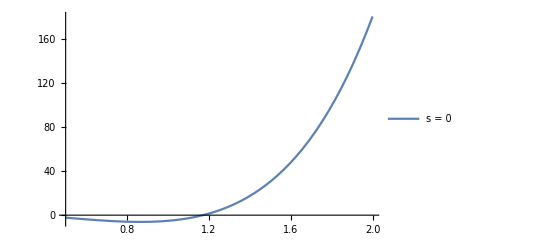

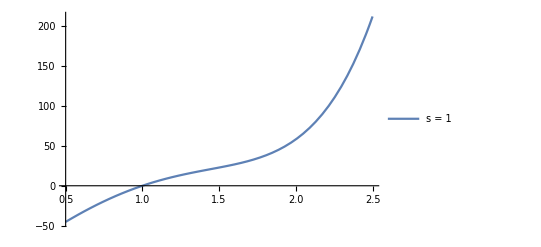

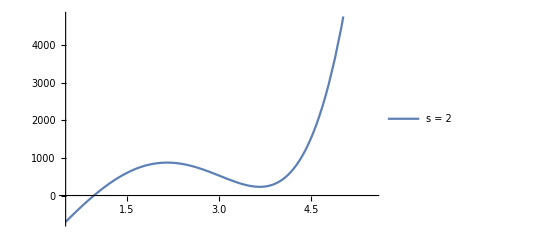

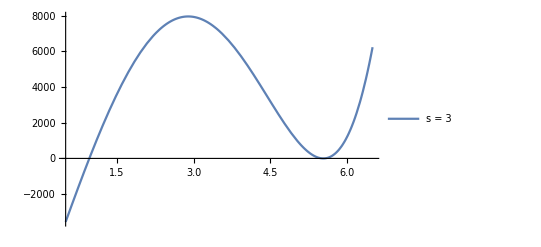

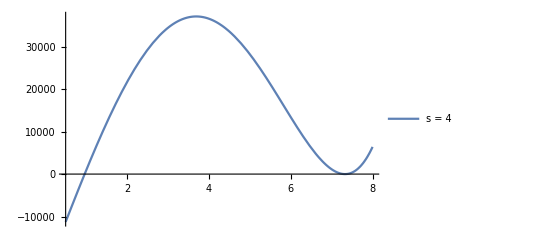

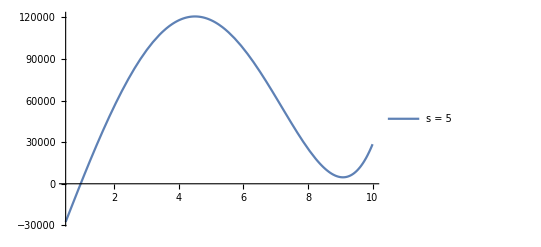

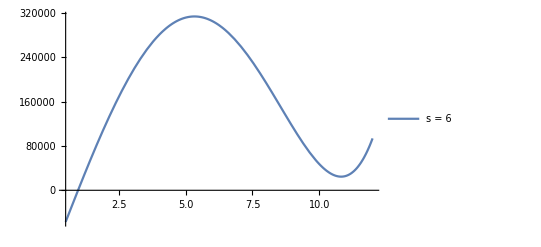

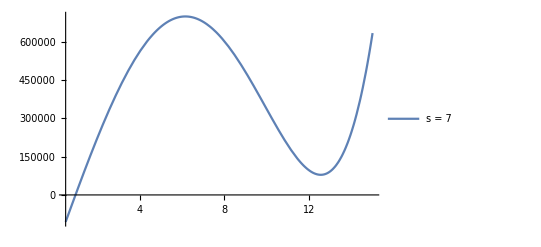

```mathematica
a = ExtremalFunctional[1.17121438980102,4.,6,4,1];
fs0[x_] := a .  mbBlocks[6, 4,0];
Plot[fs0[x], {x,0.5,2},PlotLegends->{"s = 0"}]
fs1[x_] := a .  mbBlocks[6, 4,1];
Plot[fs1[ x], {x,0.5,2.5}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[6, 4,2], {x,0.5,5.5}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[6, 4,3], {x,0.5,6.5}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[6, 4,4], {x,0.5,8.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[6, 4,5], {x,0.5,10.0}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[6, 4,6], {x,0.5,12.0},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[6, 4,7], {x,0.5,15.0},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[6, 4,8], {x,0.5,17.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[6, 4,9], {x,0.5,19.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[6, 4,10], {x,0.5,23.0},PlotLegends->{"s = 10"}]
```

### Trying out the above with max spin = 7. This does not affect the functional appreciably.

```mathematica
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.17,1.2, 0.0000001,4.,6,7, 1];
lowestBound
```

> trying: 1.185
> trying: 1.1775
> trying: 1.17375
> trying: 1.17188
> trying: 1.17094
> trying: 1.17141
> trying: 1.17117
> trying: 1.17129
> trying: 1.17123
> trying: 1.1712
> trying: 1.17122
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121
> trying: 1.17121

> objective: 0.000000423018818080755294696406774021975436571324438309251223172917771185286504573843135509193748889112399099127577139147411524444984561577925562422952154231911964886907972063078483902176880328734692569520100396093685656527295373678782050842144948778462181296517753966730447284932148599791382762694832833229181672161

```mathematica
sMax = 7;
dOrder = 6;
a = ExtremalFunctional[1.17121438980102,4.,dOrder,sMax,1];
fs0[x_] := a .  mbBlocks[dOrder, 4,0];
Plot[fs0[x], {x,0.5,2},PlotLegends->{"s = 0"}]
fs1[x_] := a .  mbBlocks[dOrder, 4,1];
Plot[fs1[ x], {x,0.5,2.5}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[dOrder, 4,2], {x,0.5,5.5}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[dOrder, 4,3], {x,0.5,6.5}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[dOrder, 4,4], {x,0.5,8.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[dOrder, 4,5], {x,0.5,10.0}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[dOrder, 4,6], {x,0.5,12.0},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[dOrder, 4,7], {x,0.5,15.0},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[dOrder, 4,8], {x,0.5,17.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[dOrder, 4,9], {x,0.5,19.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[dOrder, 4,10], {x,0.5,23.0},PlotLegends->{"s = 10"}]
```

> objective: 0.000000296722214645436311586602962236297979879035968884318589032336885984322093662499655943944114402557943061820589617765111887343568354069303968742836636976573208517269181658462115217732671857559541527856725838166045593553028871296502649296201272683557456020663282741506316532606207033461149532506014502121771903744

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
lowestBounds = Table[BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.2, 0.000001,4.,6,smax, smax],{smax,2,12,2}];
```

### Comparing functionals of derivative order = 6, at different smax.

#### The claim is that at sufficietly large smax, the functional stabilises. At order = 6, smax = 4 is enough to approximate the functional.

```mathematica
exFunctionals = Table[ExtremalFunctional[lowestBounds[[(smax)/2]],4.,6,smax,smax],{smax,2,12,2}];
```

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,0], {x,-0.1,1.7},PlotLabel->"Funtional s=0",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,2,12,2}];
```

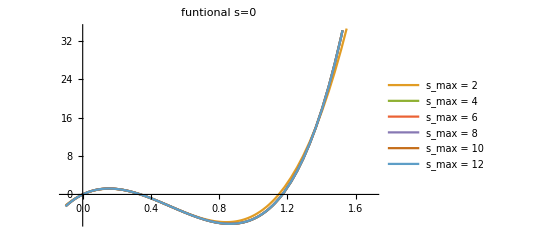

```mathematica
Show[ps]
```

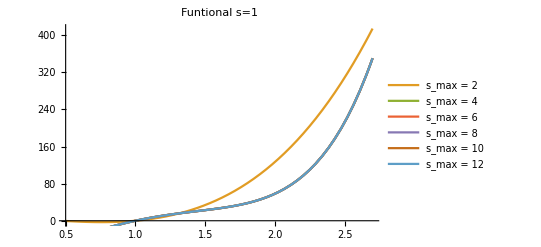

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,1], {x,0.5,2.7},PlotLabel->"Funtional s=1",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,2,12,2}];
Show[ps]
```

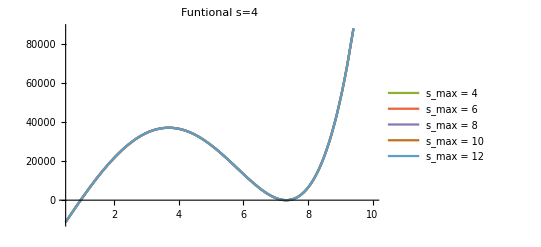

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,4], {x,0.5,10.0},PlotLabel->"Funtional s=4",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,12,2}];
Show[ps]
```

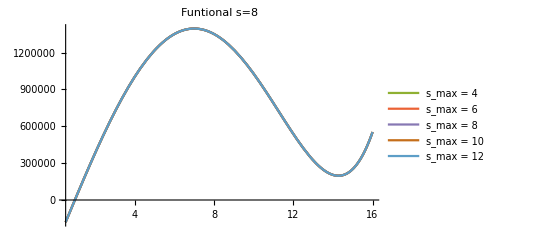

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,8], {x,0.5,16.0},PlotLabel->"Funtional s=8",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,12,2}];
Show[ps]
```

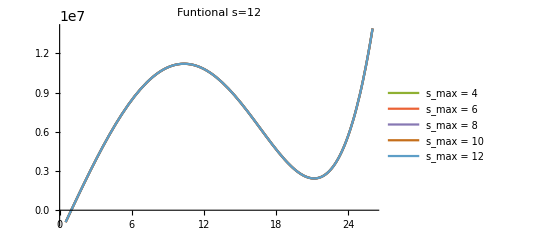

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,12], {x,0.5,26.0},PlotLabel->"Funtional s=12",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,12,2}];
Show[ps]
```

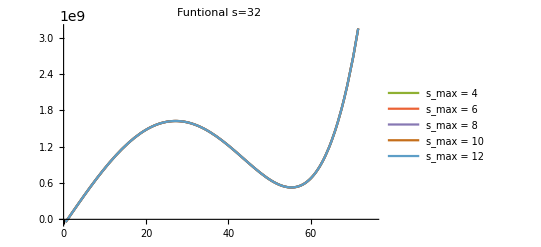

```mathematica
ps = Table[Plot[exFunctionals[[(smax)/2]] .  mbBlocks[6, 4,32], {x,0.5,75.0},PlotLabel->"Funtional s=32",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,12,2}];
Show[ps]
```

### Comparing functionals of derivative order = 9, at different smax .

```mathematica
lowestBounds = Table[BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.2, 0.000001,4.,9,smax, smax],{smax,4,18,2}];
```

```mathematica
exFunctionals9 = Table[ExtremalFunctional[lowestBounds[[(smax-2)/2]],4.,9,smax,smax],{smax,4,18,2}];
```

> objective: 0.00000406892740966025467932466878788963111625755065062961445199925993334111281922242792254853889965732626462047005551714824357464739841296438506999229957304717209211738631769695625910558432020194297722763306012024104508811806643436922788640279502964026930867754565872231981298775100453622710885164530586693865033095
> objective: 0.00000444043881674799437834733832104065473282962596136914327410692537761010445650519838272311480503431960696466164398002625816628881351077765191294749678326599231598620492737902814524962862057900426151229787920169928223141174707450765096438115390903639104927813142863504000888587868140687883836803476122352582994935
> objective: 0.000000000909007596982376178271603923606645391719732548810065050839344797580843177573302657009129178197774944521240709341111349492223039532673536830910033607261611012576032659982177022293107384464082926938659436412670537001253340215762204318325482880665655383987784687624940481964871376410564144446191366889627577997445
> objective: 0.00000130913867707644860415078565585783088163148730618654976538086466808429593918103514718519689547270771664148552268189164888122130559170337429265672740114418138645748746251498566552276572984810254413266404279681284087250240822342078801454844864450644993626027504428020803001502453702471580566287352603631435191992
> objective: 0.00000200113732520601589237791394364390092115797290694353840001453086806972238635019693983582758071591675614389419850413616640753019735658779559599631240446715180476109016469977942512717271196129963073621626333340644183144241339757607203211155914533836043419581296454754271388730159848420500791556772872940216375951
> objective: 0.00000157595700832334457030403363388268959259262739014025750205756560408927145044460706936370375155850126025457865659334626153340473681778282438889426414827599042021402579282717338197028455944074015933781424341087177475874381208743721315369256396773679099621605614290589697996796179984903188556739329780919851433967
> objective: 0.00000284615817145104332466501834639477683533631248827923477708844867103573377590090892857807548826510273844428298841168039913246202598408545583324644665361084584444645958724792653239029528758991246633410370807155123972385784447736671557015983084099572214010926910328562704173049265832139991393680388822081518297731
> objective: 0.00000146070601330981218819235564010942572885323902950764761249941375621457460764466714969654507254094069758338744716491912018152810608835954217920270491169556498094169706721363612214942991645817976982981340823833258236148239546607531226018973758762761073497877019842690144243424980500670442484656204545934196460155

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,0], {x,-0.1,3.0},PlotLabel->"Funtional s=0",PlotStyle->ColorData[97,smax/2+1], PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
```

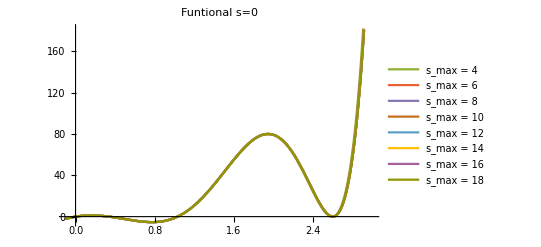

```mathematica
Show[ps]
```

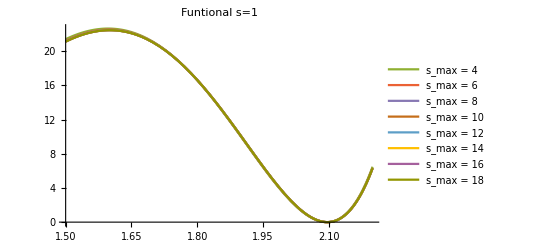

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,1], {x,1.5,2.2},PlotLabel->"Funtional s=1",PlotStyle->ColorData[97,smax/2+1],PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

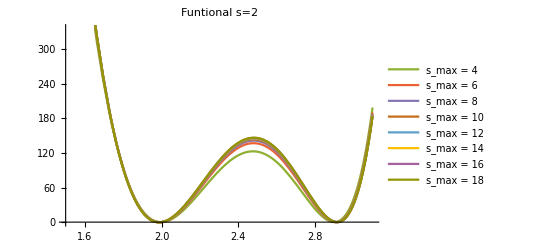

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,2], {x,1.5,3.1},PlotLabel->"Funtional s=2",PlotStyle->ColorData[97,smax/2+1],PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

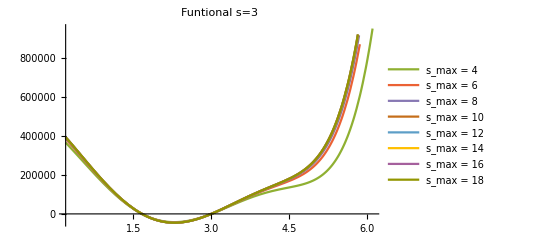

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,3], {x,0.2,6.1},PlotLabel->"Funtional s=3",PlotStyle->ColorData[97,smax/2+1],PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

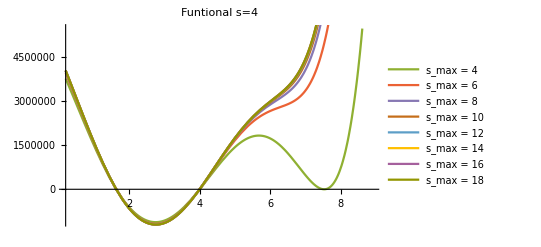

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,4], {x,0.2,8.9},PlotLabel->"Funtional s=4",PlotStyle->ColorData[97,smax/2+1],PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

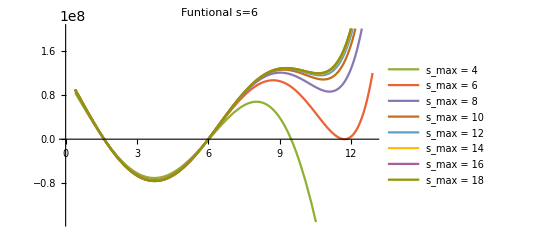

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,6], {x,0.4,12.9},PlotLabel->"Funtional s=6",PlotStyle->ColorData[97,smax/2+1],PlotRange->{-1.5*^8, 2*^8},PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,12], {x,0.2,31.0},PlotLabel->"Funtional s=12",PlotStyle->ColorData[97,smax/2+1],PlotRange->{-2.5*^11, 1.5*^11},PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
```

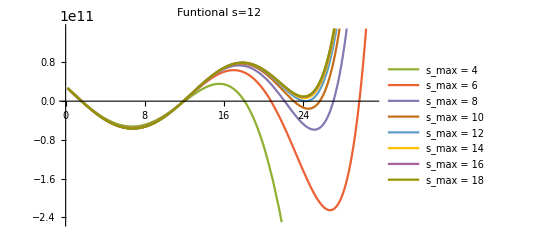

```mathematica
Show[ps]
```

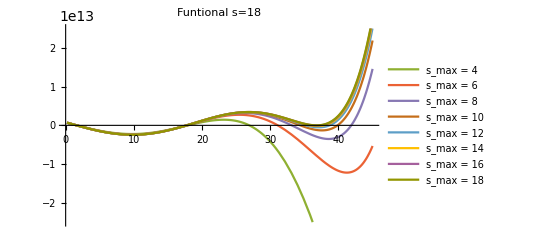

```mathematica
ps = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,18], {x,0.2,45.0},PlotLabel->"Funtional s=18",PlotStyle->ColorData[97,smax/2+1],PlotRange->{-2.5*^13, 2.5*^13}, PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

```mathematica
s = Table[Plot[exFunctionals9[[(smax-2)/2]] .  mbBlocks[9, 4.,18], {x,0.2,45.0},PlotLabel->"Funtional s=32",PlotStyle->ColorData[97,smax/2+1],PlotRange->{-2.5*^13, 2.5*^13}, PlotLegends->{StringJoin[{"s_max = ",ToString[smax]}]}],{smax,4,18,2}];
Show[ps]
```

#### At derivative order = 10, smax =7

```mathematica
BinarySearch[SolveSpinningBootstrapSDP, 0.1,2.0, 0.001,4.,10,7, 1]
```

```mathematica
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.1, 0.0000001,4.,10,7, 1];
lowestBound
```

> trying: 1.05
> trying: 1.025
> trying: 1.0375
> trying: 1.03125
> trying: 1.02813
> trying: 1.02969
> trying: 1.03047
> trying: 1.03008
> trying: 1.03027
> trying: 1.03037
> trying: 1.03032
> trying: 1.0303
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029
> trying: 1.03029

1.03029

```mathematica
dOrder =10;
sMax = 7;
a = ExtremalFunctional[1.030287265777588,4.,dOrder,sMax,0];
```

> objective: 0.000000423018818080755294696406774021975436571324438309251223172917771185286504573843135509193748889112399099127577139147411524444984561577925562422952154231911964886907972063078483902176880328734692569520100396093685656527295373678782050842144948778462181296517753966730447284932148599791382762694832833229181672161

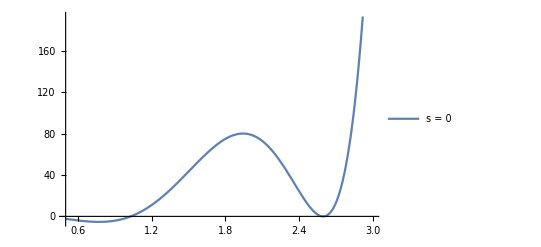

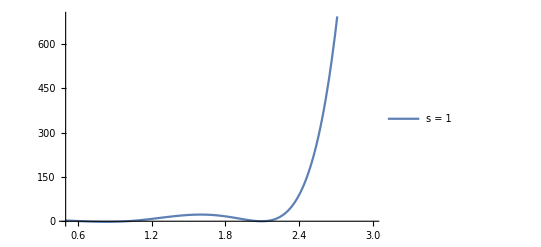

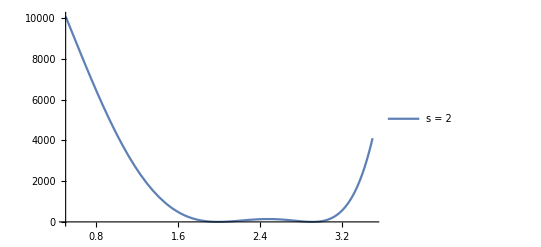

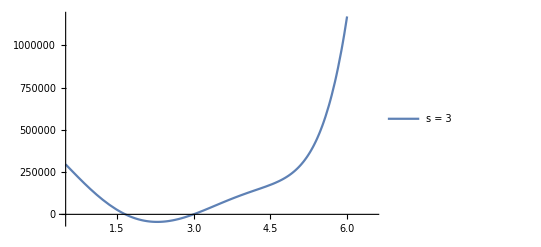

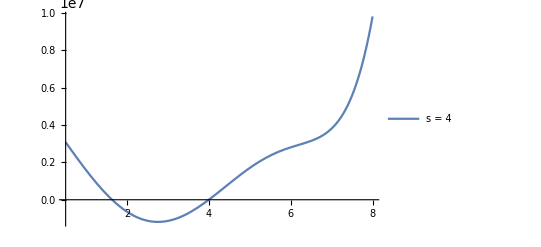

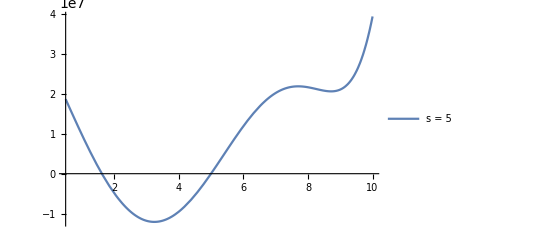

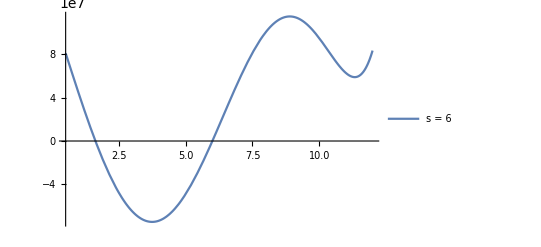

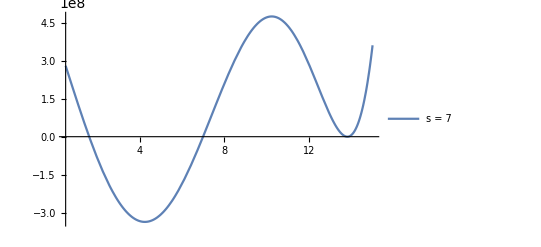

```mathematica
Plot[a .  mbBlocks[dOrder, 4,0], {x,0.5,3.0},PlotLegends->{"s = 0"}]
Plot[a .  mbBlocks[dOrder, 4,1], {x,0.5,3.0}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[dOrder, 4,2], {x,0.5,3.5}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[dOrder, 4,3], {x,0.5,6.5}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[dOrder, 4,4], {x,0.5,8.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[dOrder, 4,5], {x,0.5,10.0}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[dOrder, 4,6], {x,0.5,12.0},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[dOrder, 4,7], {x,0.5,15.0},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[dOrder, 4,8], {x,0.5,23.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[dOrder, 4,9], {x,0.5,24.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[dOrder, 4,10], {x,0.5,26.0},PlotLegends->{"s = 10"}]
Plot[a .  mbBlocks[dOrder, 4,11], {x,0.5,28.0},PlotLegends->{"s = 11"}]
Plot[a .  mbBlocks[dOrder, 4,12], {x,0.5,29.0},PlotLegends->{"s = 12"}]
Plot[a .  mbBlocks[dOrder, 4,13], {x,0.5,30.0},PlotLegends->{"s = 13"}]
```

#### At derivative order = 10, smax =10

```mathematica
dOrder =10;
sMax = 10;
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.1, 0.0000001,4.,dOrder,sMax, 2];
```

```mathematica
a = ExtremalFunctional[lowestBound,4.,dOrder,sMax,2];
```

> objective: 0.000000564266290271679104982046154957734046088805870425037224442122125251390126454095664381897915813473137120119116457226966245261649761409528868122230599633195540395798442362710331154900109095471143062696798740112140849237559277356586175279965848086466660811273294688224267962418045081552394778725182146042451999292

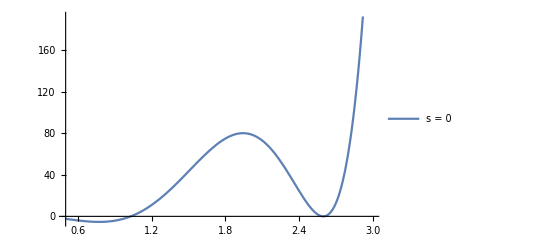

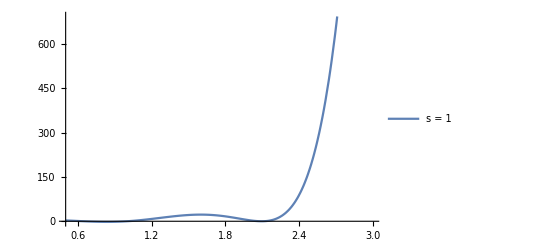

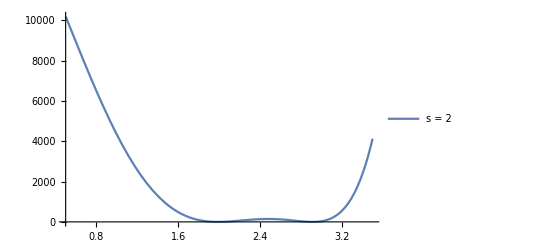

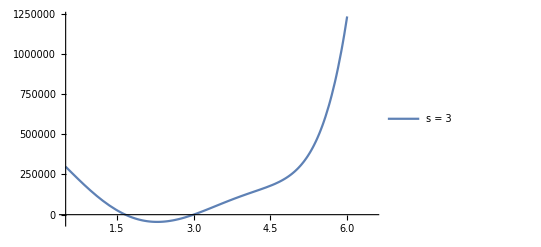

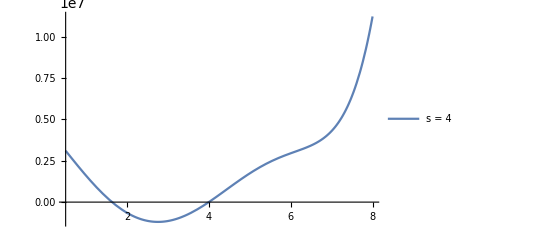

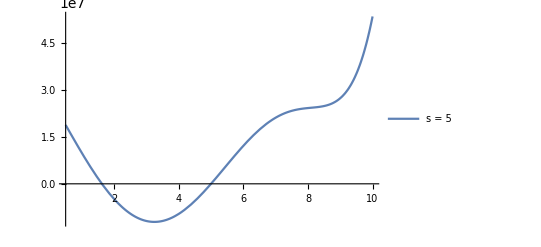

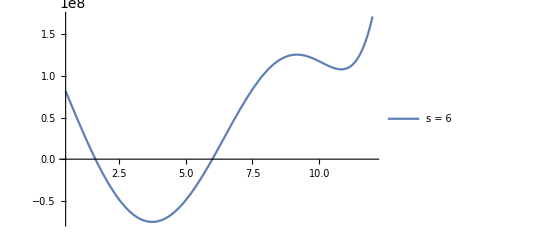

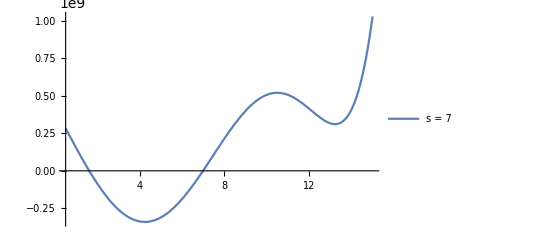

```mathematica
Plot[a .  mbBlocks[dOrder, 4,0], {x,0.5,3.0},PlotLegends->{"s = 0"}]
Plot[a .  mbBlocks[dOrder, 4,1], {x,0.5,3.0}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[dOrder, 4,2], {x,0.5,3.5}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[dOrder, 4,3], {x,0.5,6.5}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[dOrder, 4,4], {x,0.5,8.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[dOrder, 4,5], {x,0.5,10.0}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[dOrder, 4,6], {x,0.5,12.0},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[dOrder, 4,7], {x,0.5,15.0},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[dOrder, 4,8], {x,0.5,23.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[dOrder, 4,9], {x,0.5,24.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[dOrder, 4,10], {x,0.5,26.0},PlotLegends->{"s = 10"}]
Plot[a .  mbBlocks[dOrder, 4,11], {x,0.5,28.0},PlotLegends->{"s = 11"}]
Plot[a .  mbBlocks[dOrder, 4,12], {x,0.5,29.0},PlotLegends->{"s = 12"}]
Plot[a .  mbBlocks[dOrder, 4,13], {x,0.5,30.0},PlotLegends->{"s = 13"}]
```

#### At derivative order = 10, smax =13

```mathematica
dOrder =10;
sMax = 13;
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.1, 0.0000001,4.,dOrder,sMax, 3];
a = ExtremalFunctional[lowestBound,4.,dOrder,sMax,3];
```

> trying: 1.05
> trying: 1.025
> trying: 1.0375
> trying: 1.03125
> trying: 1.02813
> trying: 1.02969
> trying: 1.03047
> trying: 1.03008
> trying: 1.03027
> trying: 1.03037
> trying: 1.03042
> trying: 1.0304
> trying: 1.03038
> trying: 1.03039
> trying: 1.03039
> trying: 1.03038
> trying: 1.03039
> trying: 1.03039
> trying: 1.03039
> trying: 1.03039
> objective: 0.00000069902346745198941575554524739050336713999627952375497065364172548611755618660438576600029556531809690621144153756497621399555932673960571683619676553484288825460886335881467316622692590144667225048146229914026630249196885499095293351217013434744716807308899740625413146228855518454866783884763941839257275459

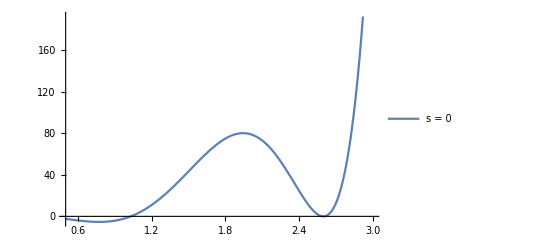

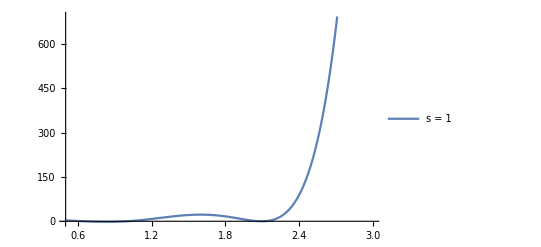

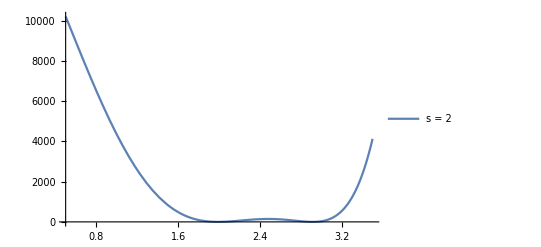

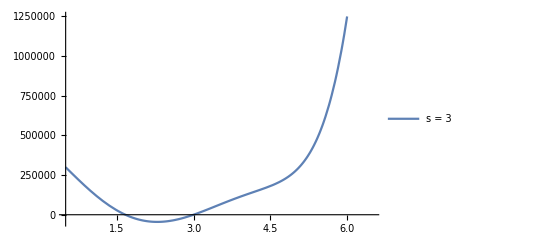

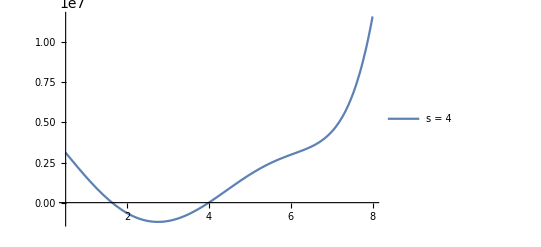

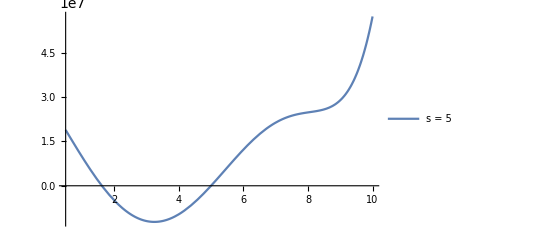

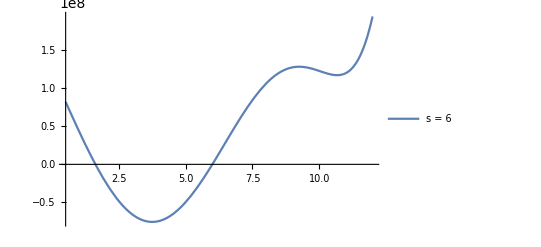

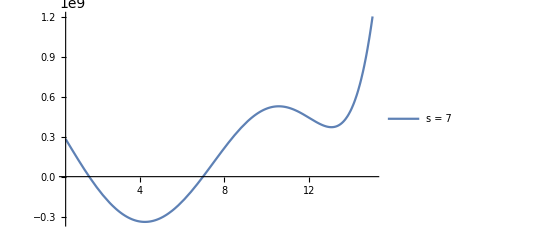

```mathematica
Plot[a .  mbBlocks[dOrder, 4,0], {x,0.5,3.0},PlotLegends->{"s = 0"}]
Plot[a .  mbBlocks[dOrder, 4,1], {x,0.5,3.0}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[dOrder, 4,2], {x,0.5,3.5}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[dOrder, 4,3], {x,0.5,6.5}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[dOrder, 4,4], {x,0.5,8.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[dOrder, 4,5], {x,0.5,10.0}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[dOrder, 4,6], {x,0.5,12.0},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[dOrder, 4,7], {x,0.5,15.0},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[dOrder, 4,8], {x,0.5,23.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[dOrder, 4,9], {x,0.5,24.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[dOrder, 4,10], {x,0.5,26.0},PlotLegends->{"s = 10"}]
Plot[a .  mbBlocks[dOrder, 4,11], {x,0.5,28.0},PlotLegends->{"s = 11"}]
Plot[a .  mbBlocks[dOrder, 4,12], {x,0.5,29.0},PlotLegends->{"s = 12"}]
Plot[a .  mbBlocks[dOrder, 4,13], {x,0.5,30.0},PlotLegends->{"s = 13"}]
Plot[a .  mbBlocks[dOrder, 4,14], {x,0.5,30.0},PlotLegends->{"s = 14"}]
Plot[a .  mbBlocks[dOrder, 4,15], {x,0.5,30.0},PlotLegends->{"s = 15"}]
```

#### At derivative order = 12, smax = 13

```mathematica
dOrder =12;
sMax = 13;
lowestBound = BinarySearchPrecision[SolveSpinningBootstrapSDP2, 1.0,1.1, 0.0000001,4.,dOrder,sMax, 4];
a = ExtremalFunctional[lowestBound,4.,dOrder,sMax,4];
```

> trying: 1.05
> trying: 1.025
> trying: 1.0125
> trying: 1.00625
> trying: 1.00938
> trying: 1.01094
> trying: 1.01172
> trying: 1.01133
> trying: 1.01113
> trying: 1.01123
> trying: 1.01128
> trying: 1.01125
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> trying: 1.01124
> objective: 0.000000146448917096837508897818965150813088689955135985212779886147431117114813408359725320374887145324798540698365267379079839411270730064947200749760720231282698934510907479619429052739338132995857367347007966740148525896536444386904809942902154190719026968740324483817627646604805249696507680542336567624530194371

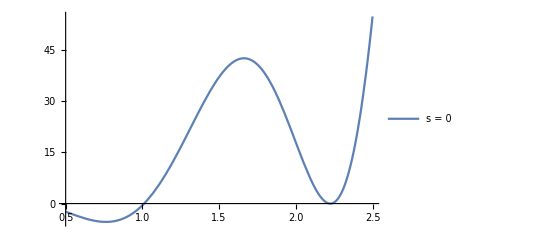

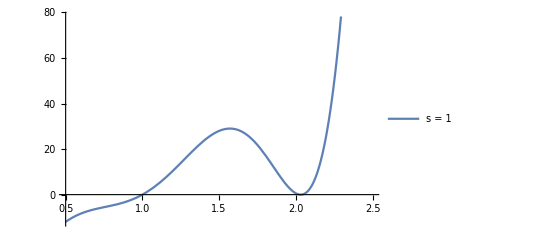

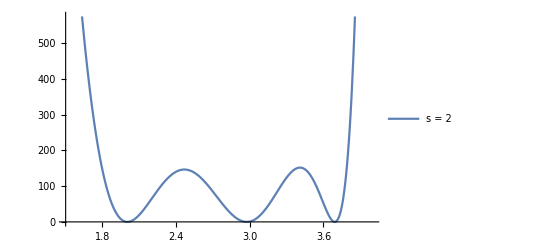

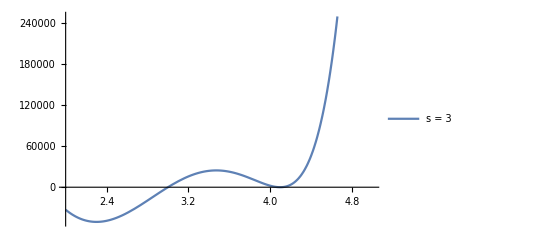

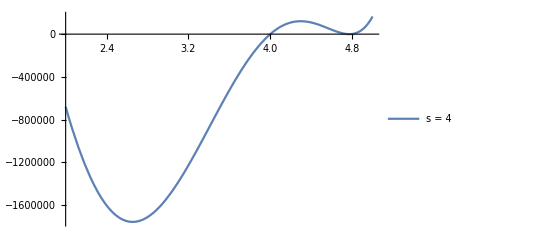

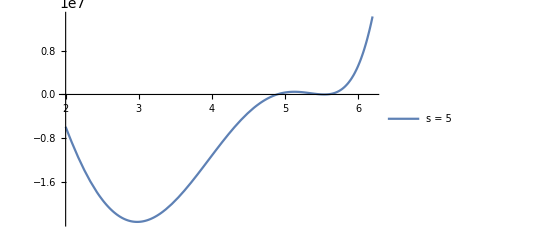

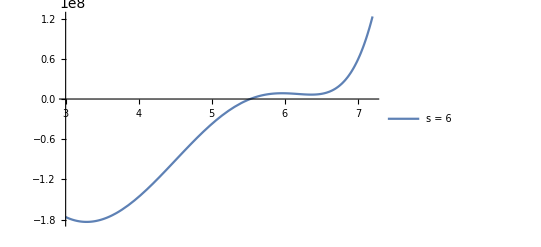

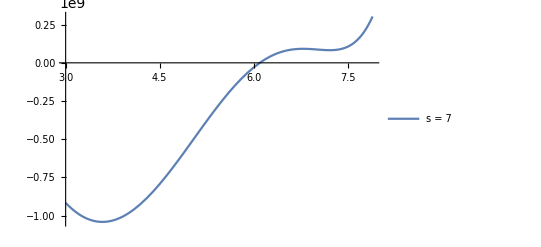

```mathematica
Plot[a .  mbBlocks[dOrder, 4,0], {x,0.5,2.5},PlotLegends->{"s = 0"}]
Plot[a .  mbBlocks[dOrder, 4,1], {x,0.5,2.5}, PlotLegends->{"s = 1"}]
Plot[a .  mbBlocks[dOrder, 4,2], {x,1.5,4.0}, PlotLegends->{"s = 2"}]
Plot[a .  mbBlocks[dOrder, 4,3], {x,2.0,5.0}, PlotLegends->{"s = 3"}]
Plot[a .  mbBlocks[dOrder, 4,4], {x,2.0,5.0}, PlotLegends->{"s = 4"}]
Plot[a .  mbBlocks[dOrder, 4,5], {x,2.0,6.2}, PlotLegends->{"s = 5"}]
Plot[a .  mbBlocks[dOrder, 4,6], {x,3.0,7.2},PlotLegends->{"s = 6"}]
Plot[a .  mbBlocks[dOrder, 4,7], {x,3.0,7.9},PlotLegends->{"s = 7"}]
Plot[a .  mbBlocks[dOrder, 4,8], {x,3.0,8.0},PlotLegends->{"s = 8"}]
Plot[a .  mbBlocks[dOrder, 4,9], {x,3.0,9.0},PlotLegends->{"s = 9"}]
Plot[a .  mbBlocks[dOrder, 4,10], {x,3.0,10.0},PlotLegends->{"s = 10"}]
Plot[a .  mbBlocks[dOrder, 4,11], {x,3.0,11.0},PlotLegends->{"s = 11"}]
Plot[a .  mbBlocks[dOrder, 4,12], {x,3.0,12.0},PlotLegends->{"s = 12"}]
Plot[a .  mbBlocks[dOrder, 4,13], {x,3.0,13.0},PlotLegends->{"s = 13"}]
Plot[a .  mbBlocks[dOrder, 4,14], {x,3.0,14.0},PlotLegends->{"s = 14"}]
Plot[a .  mbBlocks[dOrder, 4,15], {x,3.0,15.0},PlotLegends->{"s = 15"}]
```

#### Rough work beyond this point

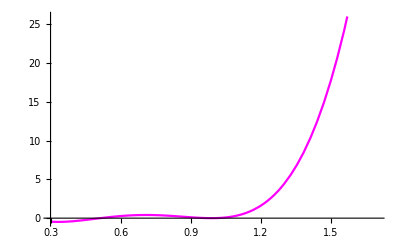

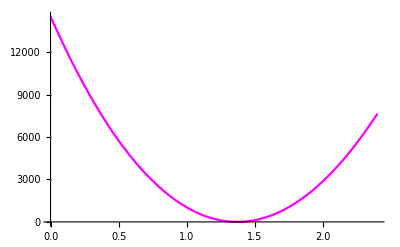

```mathematica
fs0[x_] = a .  mbBlocks0[6, 6.4];
p05 =Plot[fs0[2Pi x], {x,0.3,1.7}, PlotStyle->Magenta]
 fs1[x_] = a .  mbBlocks1[6, 6.4];
p15 =Plot[fs1[2Pi x], {x,0,2.4},PlotStyle->Magenta]
```

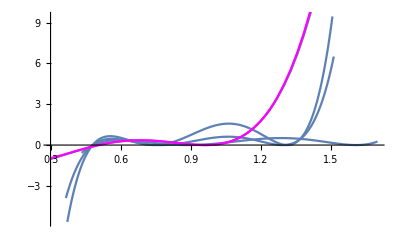

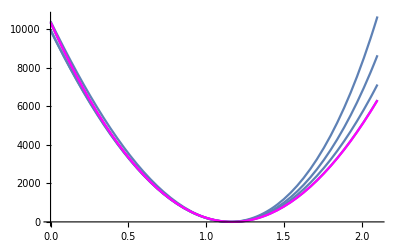

```mathematica
Show[p01,p02,p03,p04,p05]
Show[p11,p12,p13,p14,p15]
```

```mathematica
FindRoot[fs1[2Pi x] == 0 ,{x,0.4}]
```

{x→1.16938}

```mathematica
FindRoot[fs0[2Pi x] == 0 ,{x,0.1}]
 FindRoot[fs0[2Pi x] == 0 ,{x,0.5}]
 FindRoot[fs0[2Pi x] == 0 ,{x,1.5}]
```

{x→0.0254131}

{x→0.506084}

{x→0.962662}

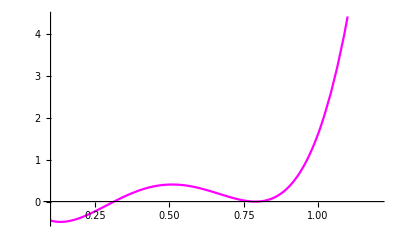

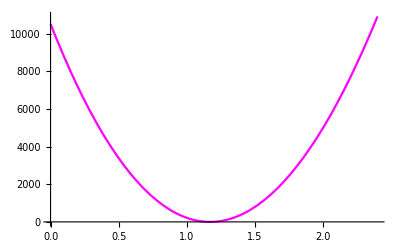

```mathematica
fs0[x_] = a .  mbBlocks0[6, 4];
p05 =Plot[fs0[2Pi x], {x,0.1,1.2}, PlotStyle->Magenta]
 fs1[x_] = a .  mbBlocks1[6, 4];
p15 =Plot[fs1[2Pi x], {x,0,2.4},PlotStyle->Magenta]
```

```mathematica
FindRoot[fs0[2Pi x] == 0 ,{x,0.1}]
 FindRoot[fs0[2Pi x] == 0 ,{x,0.5}]
 FindRoot[fs0[2Pi x] == 0 ,{x,1.5}]
 FindRoot[fs1[2Pi x] == 0 ,{x,1.5}]
```

{x→0.0171942}

{x→0.313507}

{x→0.789526}

{x→1.17097}

True

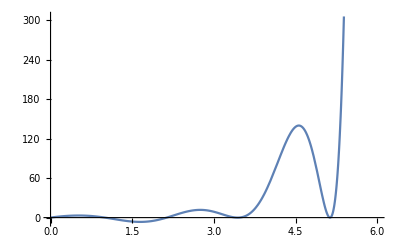

```mathematica
sdpfname= FileNameJoin[{"/Users/divyanshu/SDPbootstrap/spinless","bsl"}];
ModularBootstrapSpinnless[sdpfname,2Pi*2.1317077922680436,6,12]
```

```mathematica
FindRoot[F[2Pi x],{x,3.12}]
FindRoot[F[2Pi x],{x,4.12}]
FindRoot[F[2Pi x],{x,5.12}]
FindRoot[F[2Pi x],{x,6.12}]
FindRoot[F[2Pi x],{x,7.12}]
FindRoot[F[2Pi x],{x,8.12}]
```

{x→3.17207}

{x→4.41552}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→4.41554}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→5.87912}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→5.87911}

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→7.7695}

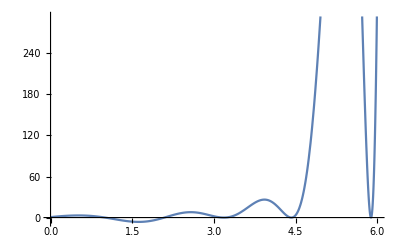

```mathematica
fullResult[[1]] = 1;
F[x_]=fullResult . N[chiralCharacterTable[10]];
Plot[F[2Pi x],{x,0,6}]
```

```mathematica
fname= FileNameJoin[{"/Users/divyanshu/SDPbootstrap/","bsl"}];
ModularBootstrapSpinning[fname,{2Pi*0.9842},6,12,0];
Run["sh boots_.sh"];
outResult = Import["/Users/divyanshu/SDPbootstrap/input_out/out.txt","List"];
a=Import["/Users/divyanshu/SDPbootstrap/input_out/y.txt","List"];
a[[1]] = 1;
outResult[1]
```